ResourceFunction["MaTeXInstall"][]

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
TempArray={0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105}
```

{0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105}

```mathematica
Tc=0.0867
```

0.0867

```mathematica
FreeEnergyA ={-84.188949,-84.2338276,-84.276402,-84.35494693,-84.46287,-84.60768692,-84.7800132,-84.987916,-85.230636,-85.5014,-85.808408,-86.148134,-86.522218,-86.92848126,-87.3788064,-87.8706998,-88.4025313,-88.966392,-89.559826,-90.17458};
```

```mathematica
FreeEnergyB = {-83.182112,-83.72774,-83.83357494,-83.955454,-84.104750498,-84.28610916,-84.496271388,-84.7386278,-85.012024,-85.3176462,-85.65702206,-86.0359088,-86.443334,-86.8846416,-87.3654322,-87.870011,-88.41158,-88.9740262,-89.56407852,-90.176425};
```

```mathematica
FreeEnergyC={-83.2250718,-83.3464892,-83.4892348,-83.6583434,-83.845658132,-84.06353,-84.31471486,-84.5902734,-84.53872,-85.2330523432,-85.6052591582,-85.99916214,-86.4269565008,-86.880179775,-87.3598152,-87.8755378,-88.407387463,-88.9697294,-89.5532455,-90.180126398};
```

```mathematica
deltaFB =( FreeEnergyB-FreeEnergyA)
```

{1.00684,0.506088,0.442827,0.399493,0.35812,0.321578,0.283742,0.249288,0.218612,0.183754,0.151386,0.112225,0.078884,0.0438397,0.0133742,0.0006888,-0.0090487,-0.0076342,-0.00425252,-0.001845}

```mathematica
deltaFC=( FreeEnergyC-FreeEnergyA)
```

{0.963877,0.887338,0.787167,0.696604,0.617212,0.544157,0.465298,0.397643,0.691916,0.268348,0.203149,0.148972,0.0952615,0.0483015,0.0189912,-0.004838,-0.00485616,-0.0033374,0.0065805,-0.0055464}

```mathematica
AvgCurvatureA ={0.086356,0.08637649,0.086721466,0.08724627,0.087914,0.08875,0.089779,0.090867,0.09194161,0.0928988,0.09375946,0.09449445,0.095199,0.0958655,0.0965585886,0.09731517,0.097048,0.09587,0.09465,0.0933848};
```

```mathematica
AvgCurvatureB={0.10278,0.10286,0.10292869,0.102899,0.10276046,0.10265122,0.10243219,0.1022195,0.10195380759,0.1016372,0.101263699,0.1008536,0.100364708,0.09978333,0.09910655,0.0981668,0.0970655,0.09588114,0.094656564,0.09338695};
```

```mathematica
AvgCurvatureC={0.10842671,0.1083257,0.1081403,0.107857,0.107484,0.106999,0.106431956,0.10575686,0.10500526878,0.104192186,0.103323224,0.10238584,0.1014168215379,0.10038726857,0.099319573,0.0982234688,0.0970662679,0.0958777,0.0946421829,0.093392159};
```

```mathematica
Dimensions[AvgCurvatureC]
```

{20}

```mathematica
betaArray = 1/TempArray;
```

```mathematica
Exp[-betaArray*deltaFB]
```

{1.87769×10^-44,2.22466×10^-15,2.42177×10^-10,1.14841×10^-7,6.54168×10^-6,0.000102266,0.000830448,0.00392756,0.0126229,0.0354023,0.0802106,0.177899,0.324032,0.557368,0.846049,0.991929,1.10577,1.08368,1.04344,1.01773}

```mathematica
Exp[-betaArray*deltaFC]
```

{1.3783×10^-42,2.03668×10^-26,8.07015×10^-18,7.92058×10^-13,1.1613×10^-9,1.7696×10^-7,8.87335×10^-6,0.00014533,9.77449×10^-7,0.00760425,0.0338501,0.101077,0.256435,0.525177,0.788684,1.05857,1.05544,1.03575,0.936313,1.05424}

```mathematica
curvxx =Table[(1+Exp[-betaArray[[n]]*deltaFB[[n]]]+Exp[-betaArray[[n]]*deltaFC[[n]]])/(AvgCurvatureC[[n]]Exp[-betaArray[[n]]*deltaFC[[n]]]+AvgCurvatureB[[n]]Exp[-betaArray[[n]]*deltaFB[[n]]]+AvgCurvatureA[[n]]),{n,1,Dimensions[TempArray][[1]]}]
```

{11.58,11.5772,11.5312,11.4618,11.3747,11.2674,11.1371,10.9995,10.8617,10.7207,10.5719,10.4164,10.281,10.1984,10.183,10.2137,10.3029,10.4301,10.5653,10.708}

```mathematica
curvxxGS=Table[1/AvgCurvatureA[[n]],{n,1,Dimensions[TempArray][[1]]}]
```

{11.58,11.5772,11.5312,11.4618,11.3748,11.2676,11.1385,11.0051,10.8765,10.7644,10.6656,10.5826,10.5043,10.4313,10.3564,10.2759,10.3042,10.4308,10.5652,10.7084}

```mathematica
TBG=Tc*0.8
```

0.06936

```mathematica
w0=1;
```

```mathematica
wTBG=0.1;
```

```mathematica
scattRateArray = Table[w0+If[TempArray[[n]]>TBG,wTBG(TempArray[[n]]-TBG)/TBG,0],{n,1,Dimensions[TempArray][[1]]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1.00092,1.00813,1.01534,1.02255,1.02976,1.03697,1.04418,1.05138}

```mathematica
scattRateArray2=1+0.1 TempArray/Tc
```

{1.01153,1.0173,1.02307,1.02884,1.0346,1.04037,1.04614,1.0519,1.05767,1.06344,1.0692,1.07497,1.08074,1.08651,1.09227,1.09804,1.10381,1.10957,1.11534,1.12111}

```mathematica
ρxx=curvxx*scattRateArray
```

{11.58,11.5772,11.5312,11.4618,11.3747,11.2674,11.1371,10.9995,10.8617,10.7207,10.5719,10.4164,10.2905,10.2814,10.3392,10.4441,10.6095,10.8157,11.032,11.2582}

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->24};
```

```mathematica
legend=SwatchLegend[{Blue,Green, Orange},{MaTeX["\\text{1 pocket}",Magnification->1.45],MaTeX["\\text{2 pocket}",Magnification->1.45],MaTeX["\\text{3 pocket}",Magnification->1.45]},LegendMarkers->Graphics[{EdgeForm[Black],Disk[]}],LegendMarkerSize->{16,16}];
```

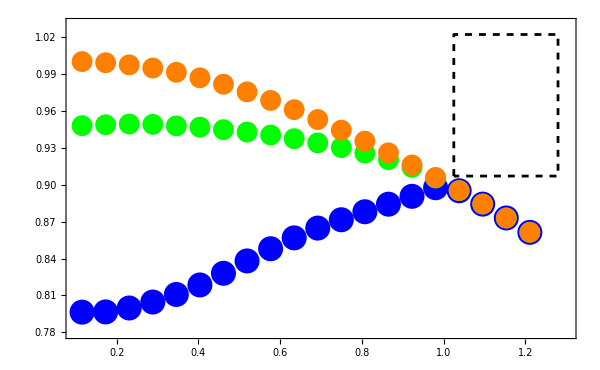

```mathematica
Legended[Show[ListPlot[Transpose@{TempArray/Tc,AvgCurvatureA/Max[AvgCurvatureC]},PlotStyle->{Blue,PointSize[0.03]},PlotRange->{{0.1,1.3},{0.78,1.03}}],ListPlot[Transpose@{TempArray/Tc,AvgCurvatureB/Max[AvgCurvatureC]},PlotStyle->{Green,PointSize[0.025]},BaseStyle->MaTeX],
ListPlot[Transpose@{TempArray/Tc,AvgCurvatureC/Max[AvgCurvatureC]},PlotStyle->{Orange,PointSize[0.025]},BaseStyle->MaTeX],
ListPlot[{{1.025,0.907},{1.025,1.022},{1.28,1.022},{1.28,0.907},{1.025,0.907}},Joined-> True,PlotStyle-> {Black,Dashed}],
Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2],MaTeX["\\left \\langle \\frac{\\partial^2 \\epsilon}{\\partial k^2} \\right \\rangle",Magnification->2]},
BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,RotateLabel-> False,ImageSize->600],Placed[legend,Scaled[{0.88,0.75}]]]
```

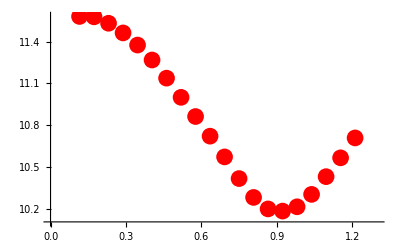

```mathematica
ListPlot[Transpose@{TempArray/Tc,curvxx},PlotStyle->{Red,PointSize[0.03]},PlotRange->{{0,1.3},Automatic}]
```

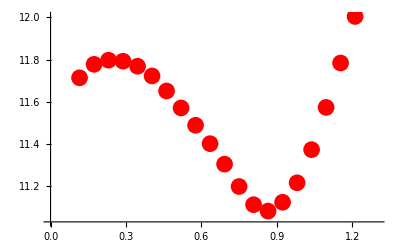

```mathematica
p0=ListPlot[Transpose@{TempArray/Tc,scattRateArray2*curvxx},PlotStyle->{Red,PointSize[0.03]},PlotRange->{{0,1.3},Automatic}]
```

```mathematica
displayLaTeX[string_]:=DisplayForm[ToBoxes@TraditionalForm@ToExpression[string,TeXForm,HoldForm]]
```

```mathematica
Min[ρxx]
```

10.2814

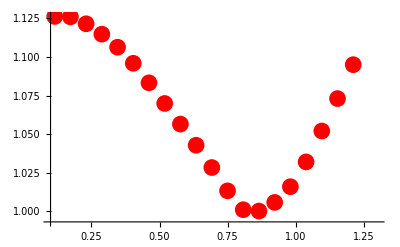

```mathematica
p1=ListPlot[Transpose@{TempArray/Tc,ρxx/Min[ρxx]},PlotStyle->{Red,PointSize[0.03]},PlotRange->{{0.1,1.3},All}]
```

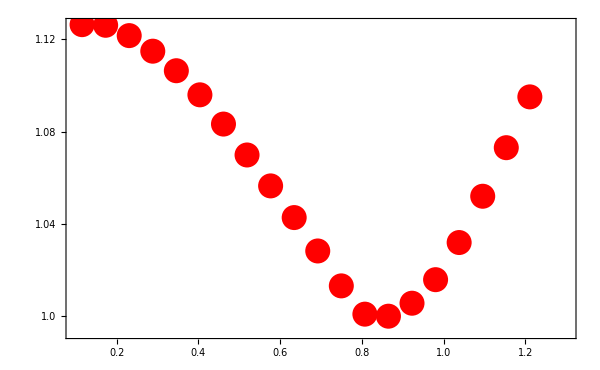

```mathematica
Show[p1,FrameTicks-> {{{{1.0,"1.0"},1.04,1.08,1.12},None},{Automatic,None}},Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2],MaTeX["\\frac{\\rho_{xx}}{\\rho_\\text{Min}}",Magnification->2]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> texStyle,RotateLabel-> False,ImageSize->600]
```